## 1. Short note of NOM

This notebook, prepared using Mathematica 13.0, includes the implementation of the implicit NOM (Nonlocal Operator Method). Additionally, a simple example of a 2D cantilever beam is provided. If you have any questions related to this notebook, please feel free to ask. You can reach me at huilongren2012@gmail.com.

## Brief introduction of NOM

Nonlocal operator method can be viewed as the generalization of non-ordinary state based peridynamics (NOSBPD). Interestingly,  smoothed particle hydrodynamics  (SPH) in solid is quite similar to NOSBPD. Based on the duality concept, dual-horizon PD and dual-support SPH could be developed very similarly. This implementation incorporates both DS-SPH, DH-PD.
NOSBPD vs SPH: 
PD:-Graphics-
   zero-energy functional in PD
 -Graphics-
SPH:-Graphics-, -Graphics-,-Graphics-,-Graphics-
zero-energy functional in SPH
 -Graphics-
-Graphics-

## Theoretical derivation of implicit NOM in 2D

Independent variables：{u,ux,uy,v,vx,vy}; ux is the derivative of u with respect to x. u:=u[x,y]
(*Calculate the gradient via Taylor series expansion*)
The first-order Taylor series expansion of u':=u[x',y'] on [x,y]:
u'=u+{ux,uy}.{rx,ry};where rx，ry are the relative coordinates between u'and u，i.e. {rx,ry}=（x'-x,y'-y）.
→ (u'-u).{rx,ry}={ux,uy}.{rx,ry}⊗{rx,ry}={ux,uy}.{{rx^2,rx ry},{rx ry,ry^2}}
weighted Integration in support：w(r) weight function，r=Sqrt[rx.b2+ry.b2];
∫_H w(r)(u'-u){rx,ry} dV={ux,uy} ∫_H w(r){{rx.b2,rx ry},{rx ry,ry.b2}}dV
The nonlocal gradient is obtained with some manipulation：
{ux,uy}=∫_H w(r)(u'-u){rx,ry} dV.[ ∫_H w(r){{rx.b2,rx ry},{rx ry,ry.b2}}dV]^-1
When the domain is discretized into particles, the discrete form of {ux,uy} becomes
{ux_i,uy_i}=∑_j w(r_ij)(u_j-u_i){rxj,ryj} V_j.[ ∑_j w(r_ij){{rxj.b2,rxj ryj},{rxj ryj,ryj.b2}}V_j]^-1
where Vj is the volume of particle j, {rxj,ryj}={xj-xi,yj-yi}.

Assuming that the particles in support/horizon is denoted by： H={i,j1,j2,j3,..,jn}. 

Let R_j=w(r_ij){rxj,ryj} V_j.[ ∑_j w(r_ij){{rxj.b2,rxj ryj},{rxj ryj,ryj.b2}}V_j]^-1={rx_j,ry_j} in 2D.
 Then {ux_i,uy_i}=∑_j (u_j-u_i)(rx_j,ry_j) in 2D
The matrix form  of (uxᵢ,uyᵢ ) is
{ux_i,uy_i}=(-∑_j rx_j | rx_j1 | ... | rx_jn
-∑_j ry_j | ry_j1 | ... | ry_jn)(u_i
u_j1
.
u_jn)=B_i U_i in 2D
GradU_i=(ux | uy
vx | vy)=(-∑_j rx_j | rx_j1 | ... | rx_jn
-∑_j ry_j | ry_j1 | ... | ry_jn)(u_i v_i
u_j1 v_j1
.
u_jn v_jn)=B_i (U_i V_i) in 2D
Or  in vectorial form
d𝕦=(ux_i
uy_i
vx_i
vy_i)=(-∑_j rx_j | □ | rx_j1 | □ | . | . | rx_jn | □
-∑_j ry_j | □ | ry_j1 | □ | . | . | ry_jn | □
□ | -∑_j rx_j | □ | rx_j1 | . | . | □ | rx_jn
□ | -∑_j ry_j | □ | ry_j1 | . | . | □ | ry_jn)(u_i
v_i
u_j1
v_j1
.
.
u_jn
v_jn)=𝔹_i 𝕦_i in 2D
where d𝕦 is the vectorial form of deformation gradient of particle i，𝔹_i is operator matrix，𝕦i is the unknown vector in support. Operator matrix is similar to the strain matrix in FEM. 
(*strain tensor ϵ=1/2(GradU+GradUᵀ),stress tensor σ=D :ϵ*)
(*Strain energy density  𝔽=1/2 σ:ϵ=1/2 ϵ:D :ϵ=1/2d𝕦ᵀ.𝔻.d𝕦, ∂_d𝕦 𝔽=𝔻.d𝕦, ∂_𝕦_i d𝕦=𝔹_i ᵀ*)
(*-Graphics-*)
(*-Graphics-*)
(*-Graphics-*)
(*-Graphics-*)
The internal force density vector for particles in i's support is ℝ_i=∂_𝕦_i 𝔽_i=∂_𝕦_i d𝕦∂_d𝕦 𝔽_i =𝔹_i ᵀ.𝔻.d𝕦, Tangent stiffness matrix 𝕂_i=∂_𝕦_i ℝ_i=𝔹_i ᵀ.𝔻.∂_𝕦_i d𝕦=𝔹_i ᵀ.𝔻.𝔹_i
The strain energy in the domain is
𝔽=∑_i 𝔽_i V_i, V_i is the volume attached to particle i
The global internal forces are
ℝ=∑_i ∂_𝕦_i 𝔽_i V_i=∑_i ℝ_i V_i=∑_i 𝔹_i ᵀ.𝔻.d𝕦_i V_i
The global tangent stiffness matrix is
𝕂=∑_i ∂_𝕦_i ℝ_i V_i=∑_i 𝔹_i ᵀ.𝔻.𝔹_i V_i
Operator energy functional for linear completeness. Without the linear completeness, NOM suffers from the  zero energy mode.
𝔽^hg=μ/m ∫_H w(r_ij) (((u_j-u_i)-Gradu.r_ij).b2+((v_j-v_i)-Gradv.r_ij).b2)dV_j
≈μ/m_i∑_j w(r_ij) (((u_j-u_i)-Gradu.r_ij).b2+((v_j-v_i)-Gradv.r_ij).b2)V_j
Or 
𝔽^hg=μ/mk(∫_s w(r_ij)( (u_j-u_i)^2+(v_j-v_i)^2)dV_j-GradU:GradU K)≈μ/mk(∑_j w(r_ij)( (u_j-u_i)^2+(v_j-v_i)^2)V_j-GradU:GradU K), where K=∑_j w(r_ij) r_ij⊗ r_ij V_j
(*du2d={ux,uy,vx,vy};

(*FFK2=1/2Total[{{ux,uy},{vx,vy}}({{ux,uy},{vx,vy}}.{{k11,k12},{k12,k22}}),-1]*)

1/2 (ux (k11 ux+k12 uy)+uy (k12 ux+k22 uy)+vx (k11 vx+k12 vy)+vy (k12 vx+k22 vy))

(*D[FFK2,{du2d,1}]//Simplify*)

{k11 ux+k12 uy,k12 ux+k22 uy,k11 vx+k12 vy,k12 vx+k22 vy}

(*D[FFK2,{du2d,2}]//Simplify//MatrixForm*)

(k11 | k12 | 0 | 0
k12 | k22 | 0 | 0
0 | 0 | k11 | k12
0 | 0 | k12 | k22)

(*D[1/2((u_j-u_i)^2+(v_j-v_i)^2),{{u_i,v_i,u_j,v_j},2}]//MatrixForm*)

(1 | 0 | -1 | 0
0 | 1 | 0 | -1
-1 | 0 | 1 | 0
0 | -1 | 0 | 1)

(*In 2D,
F^hg=1/2μ/mk(∑_j w(r_ij)( (u_j-u_i)^2+(v_j-v_i)^2)V_j-GradU:GradU K)
=1/2 μ/mk[ 𝕦_i ᵀ(∑_j I_j | -I_j1 | ... | -I_jn
-I_j1 | I_j1 | 0 | 0
. | 0 | . | 0
-I_jn | 0 | 0 | I_jn)𝕦_i-d𝕦_i ᵀ.(K_i | 0
0 | K_i).d𝕦_i] 
where I_j=w(r_ij) V_j diag[1,1]; Ki=(k11 | k12
k12 | k22)*)

(*
(𝕂^hg)_i=∂_(𝕦_i 𝕦_i) 𝔽_i=μ/mk((∑_j I_j | -I_j1 | ... | -I_jn
-I_j1 | I_j1 | 0 | 0
. | 0 | . | 0
-I_jn | 0 | 0 | I_jn)-𝔹_i ᵀ.(K_i | 0
0 | K_i).𝔹_i ᵀ) in 2D
𝕂^hg=∑_i (𝕂^hg)_i V_i*)

(*Global tangent stiffness matrix:*)

(*𝕂=∑_i V_i(𝔹_i ᵀ.𝔻.𝔹_i+μ/mk((∑_j I_j | -I_j1 | ... | -I_jn
-I_j1 | I_j1 | 0 | 0
. | 0 | . | 0
-I_jn | 0 | 0 | I_jn)-𝔹_i ᵀ.(K_i | 0
0 | K_i).𝔹_i))*)

(*where mk=Tr[K_i]*)

-Graphics-
                                             Flow chart of NOM

## 2. Functions in implicit NOM

## Boundary conditions and matrix assembly

```mathematica
SetAttributes[DirichletApply,HoldAll];
SetAttributes[NeumannApply,HoldFirst];
SparseDiag[a_List]:=SparseArray[{{i_,i_}:>a[[i]]},Length[a]];
SparseDiag[a_List,ia_List,n_]:=Block[{b},b={ia,ia}ᵀ;SparseArray[b->a,{n,n}]];
DirichletApply[Ksp_,Rsp_,pL_,pen_,scale_:1.0]:=Module[{pi,tk,tk2},tk=Diagonal[Ksp]//Normal;
tk2=tk;
tk2[[pL[[1]]]]*=(pen+1.);
tk2-=tk;
Ksp+=SparseDiag[tk2];
Do[pi=pL⟦1,i⟧;Rsp⟦pi⟧=tk2[[pi]] pL⟦2,i⟧ scale,{i,Length[pL⟦1⟧]}];];
NeumannApply[Rsp_,pL_,scale_:1.0]:=Module[{},Rsp⟦pL⟦1⟧⟧+=pL⟦2⟧ scale;];
FindPoints[v1_List,xmin_List,xmax_List,show_:False]:=Module[{ilist={},y,r,ndim=Length[v1[[1]]],len=Length[v1]},Do[If[LessThan2[v1[[i]],xmax]&& LessThan2[xmin,v1[[i]]],AppendTo[ilist,i]],{i,len}];
If[show,If[ Length[v1[[1]]]==2,Print[ListPlot[v1[[ilist]],DataRange->Automatic]]];If[ Length[v1[[1]]]==3,Print[ListPointPlot3D[v1[[ilist]]],DataRange->Full]]];
ilist];
LessThan2[v1_List,v2_List]:=Module[{p=True},Do[If[v1[[i]]> v2[[i]],p=False;Break[]],{i,Length[v1]}];Return[p]];
```

```mathematica
(*BHgmatrix calculates the operator matrix for all first-order partial derivatives and tangent stiffness matrix for the operator energy functional. The tangent stiffness matrix is required for numerical stability*)
BHgmatrix[coordi_List,WeiF_,voli_List]:=Block[{num=Length[coordi],ndim=Length[coordi[[1]]],bmat,kmat,hgmat,invk,xi,vw,ri,Ri,i1,i2,I1,I2},bmat=ConstantArray[0.,{ndim ndim,ndim num}];hgmat=ConstantArray[0.,{ndim num,ndim num}];kmat=ConstantArray[0.,{ndim,ndim}];
Do[xi=coordi[[j]]-coordi[[1]];ri=Sqrt[xi.xi];vw=voli[[j]]WeiF[ri];kmat+= vw TensorProduct[xi,xi];
i1=ndim(j-1)+1;i2=ndim j;
I1=vw IdentityMatrix[ndim];
(*I1=vw ConstantArray[1.,{ndim,ndim}];*)
hgmat[[1;;ndim,1;;ndim]]+=I1;hgmat[[1;;ndim,i1;;i2]]=-I1;
hgmat[[i1;;i2,1;;ndim]]=-I1;
hgmat[[i1;;i2,i1;;i2]]=I1,{j,2,num}];
invk=Inverse[kmat];
Do[xi=coordi[[j]]-coordi[[1]];ri=Sqrt[xi.xi];Ri=voli[[j]] WeiF[ri] invk.xi;
Do[bmat[[ndim(k-1)+1;;k ndim,k]]-=Ri;bmat[[ndim(k-1)+1;;k ndim,ndim (j-1)+k]]=Ri,{k,ndim}];
,{j,2,num}];
I2=ConstantArray[0.,{ndim ndim,ndim ndim}];
Do[I2[[j ndim+1;;(j+1)ndim,j ndim+1;;(j+1)ndim]]=kmat,{j,0,ndim-1}];
hgmat-=bmatᵀ.I2.bmat;
hgmat/=Tr[kmat];
{bmat,hgmat}
];
(*Material matrix*)
Dmat[Es_,mu_,type_:3(*1,plane stress,2,plane strain,3,3D*)]:=Block[{dmat,ndim,l1,l2},If[type==1,(*plane stress*)Return[Es/(1.-mu^2){{1.,0.,0.,mu},{0.,(1.-mu)/2,(1.-mu)/2,0.},{0.,(1.-mu)/2,(1.-mu)/2,0.},{mu,0.,0.,1.}}]];
If[type==2,(*plane strain*)
Return[Es/(1.-2mu)/(1.+mu){{1.-mu,0.,0.,mu},{0.,0.5-mu,0.5-mu,0.},{0.,0.5-mu,0.5-mu,0.},{mu,0.,0.,1.-mu}}]];
(*for 3D*)
l1=Es mu/((1.+mu)(1.-2mu));l2=Es/2./(1.+mu);
{{l1+2 l2,0.,0.,0.,l1,0.,0.,0.,l1},{0.,l2,0.,l2,0.,0.,0.,0.,0.},{0.,0.,l2,0.,0.,0.,l2,0.,0.},{0.,l2,0.,l2,0.,0.,0.,0.,0.},{l1,0.,0.,0.,l1+2l2,0.,0.,0.,l1},{0.,0.,0.,0.,0.,l2,0.,l2,0.},{0.,0.,l2,0.,0.,0.,l2,0.,0.},{0.,0.,0.,0.,0.,l2,0.,l2,0.},{l1,0.,0.,0.,l1,0.,0.,0.,l1+2l2}}
];(*material matrix form for material 4-order tensor*)
Kmatrix[pvol_,bmat_,hgmat_,Es_,mu_,etype_:3,pen_:0.2]:=pvol(pen Es hgmat+bmatᵀ.Dmat[Es,mu,etype].bmat);
Kmatrix2[pvol_,bmat_,hgmat_,Es_,mu_,etype_:3,pen_:0.2]:={pvol(bmatᵀ.Dmat[Es,mu,etype].bmat),pvol pen Es hgmat};(*tangent stiffness matrix for one particle*)
NeiIIndex[NeiI_List,udim_]:=Module[{n2,n3},n2=ConstantArray[0,udim Length[NeiI]];n3=udim (NeiI-1);Do[n2[[i;;-1;;udim]]=n3+i,{i,udim}];n2];(*global index for the tangent stiffness matrix of one particle*)

GradientOfParticle[coordi_List,WeiF_,voli_List,uvwi_List]:=Block[{num=Length[coordi],ndim=Length[coordi[[1]]],bmat,kmat,invk,xi,vw,ri,Ri,i1,i2,I1,I2},bmat=ConstantArray[0.,{ndim ndim,ndim num}];kmat=ConstantArray[0.,{ndim,ndim}];
Do[xi=coordi[[j]]-coordi[[1]];ri=Sqrt[xi.xi];vw=voli[[j]]WeiF[ri];kmat+= vw TensorProduct[xi,xi];
(*I1=vw ConstantArray[1.,{ndim,ndim}];*)
,{j,2,num}];
invk=Inverse[kmat];
Do[xi=coordi[[j]]-coordi[[1]];ri=Sqrt[xi.xi];Ri=voli[[j]] WeiF[ri] invk.xi;
Do[bmat[[ndim(k-1)+1;;k ndim,k]]-=Ri;bmat[[ndim(k-1)+1;;k ndim,ndim (j-1)+k]]=Ri,{k,ndim}];
,{j,2,num}];
(*(*return dudx,dudy,dvdx,dvdy*)*)
bmat.Flatten[uvwi]
];
```

## Convert region into a list of points.

```mathematica
(*discretize domain into list of particles/points*)
GridDomain[xmin_,xmax_,dx_]:=Block[{ndim=Length[xmin],nx=Ceiling[(xmax-xmin)/dx],dx2,res},
dx2=(xmax-xmin)/nx;
If[ndim==2,res=Table[{i,j},{i,0,nx[[1]]},{j,0,nx[[2]]}]];
If[ndim==3,res=Table[{i,j,k},{i,0,nx[[1]]},{j,0,nx[[2]]},{k,0,nx[[3]]}]];
res=Flatten[res];
res=ArrayReshape[res,{Length[res]/ndim,ndim}];
Do[res[[All,i]]*=dx2[[i]],{i,ndim}];Do[res[[i]]+=xmin,{i,Length[res]}];res];
```

```mathematica
MyPlot[coord_List,u_List]:=Module[{Nnode=Length[coord],ndim=Length[coord[[1]]],xyz={}},
If[Length[coord]≠Length[u],Print["Error, length(u) should be equal to Length(coord)"];Abort[]];
xyz=ConstantArray[0.,{Nnode,ndim+1}];xyz[[All,1;;ndim]]=coord;xyz[[All,ndim+1]]=u;
ListPlot3D[xyz,Axes->True,AxesLabel->Table[i,{i,1,ndim}],BoxRatios->Automatic]];
Vector2Matrix[uv_List,udim_Integer]:=Module[{m},If[udim==1,m=uv;Return[m]];m=ConstantArray[0.,{Length[uv]/udim,udim}];
 Do[m[[i]]=uv[[udim (i-1)+1;;udim i]],{i,Length[m]}];m];
```

## Mesh-related functions.

```mathematica
Needs["NDSolve`FEM`"]
MyDelaunayMesh[coord_]:=Block[{mm,mm2,ndim},ndim=Length[coord[[1]]];
If[ndim<2 || ndim>3,Print["Error, delaunayMesh only applies for 2D and 3D"];Abort[];];
mm=DelaunayMesh[coord];mm2=If[ndim==2,Cases[MeshCells[mm,2],Polygon[x_]:>x,-1],Cases[MeshCells[mm,3],Tetrahedron[x_]:>x,-1]];Abaqus2Mesh[coord,mm2]];
MyDelaunayMesh[coord_,uvw_]:=Block[{mm,mm2,ndim=Length[coord[[1]]]},mm=DelaunayMesh[coord];mm2=If[ndim==2,Cases[MeshCells[mm,2],Polygon[x_]:>x,-1],Cases[MeshCells[mm,3],Tetrahedron[x_]:>x,-1]];Abaqus2Mesh[coord+uvw,mm2]];
Abaqus2Mesh[coord_,mesh_]:=Block[{ec,el={}},ec=ElementClassify[mesh,Length[coord[[1]]]];
If[Length[ec[[1]]]>0,AppendTo[el,TriangleElement[mesh[[ec[[1]]]]]]];
If[Length[ec[[2]]]>0,AppendTo[el,QuadElement[mesh[[ec[[2]]]]]]];
If[Length[ec[[3]]]>0,AppendTo[el,TetrahedronElement[mesh[[ec[[3]]]]]]];
If[Length[ec[[4]]]>0,AppendTo[el,HexahedronElement[mesh[[ec[[4]]]]]]];
ToElementMesh["Coordinates"->coord,"MeshElements"->el]];
ElementClassifyEc[len_,n_]:=If[n==2, If[len==3 || len==6,1,2],If[len==4||len==10,3,4]];
ElementClassify[mesh_,ndim_]:=Block[{pos=ConstantArray[0,Length[mesh]],toqh={{},{},{},{}}},Do[pos[[i]]=ElementClassifyEc[Length[mesh[[i]]],ndim];,{i,Length[mesh]}];toqh[[1]]=Flatten[Position[pos,1]];toqh[[2]]=Flatten[Position[pos,2]];toqh[[3]]=Flatten[Position[pos,3]];toqh[[4]]=Flatten[Position[pos,4]];toqh];
```

```mathematica
ParseAbaqusFile::usage="{nodes,elements,sets}=ParseAbaqusFile[FilePath];it can only read keywords: *node, *element, *set. Before processing the file, please convert the *elset to *set and *nset to *set in the input file";
ParseAbaqusFile[file_String]:=Module[{i,j,k,node,element,setList,oneSet,starList,starLine,tlineStart,tlineEnd,tline,strings,String2List, i1,i2,len,pair,ei,j1},
If[FileExtension[file]≠"inp",Print["Error,the file should be Abaqus keyword file .inp"];Return[];];
strings=ReadList[file,String];If[strings==$Failed,Print["Error,file not found"];Return[]];i=Dimensions[strings][[1]];node={};
element={};
setList={};
starList={};
Do[If[StringStartsQ[strings[[j]],"*"]&&!StringStartsQ[strings[[j]],{"**","$"}],AppendTo[starList,j]],{j,i}];
String2List[str_String]:=Module[{sl,s2},s2=StringReplace[str,{"E","e"}->"*^"];sl=StringSplit[s2,{","," "}];
DeleteCases[ToExpression[sl],Null]];
Do[starLine=ToLowerCase[strings[[starList[[j]]]]];
tlineStart=starList[[j]]+1;tlineEnd=starList[[j+1]]-1;
Which[StringStartsQ[starLine,"*node"],Do[tline=strings[[k]];
If[!StringStartsQ[tline,"*"],AppendTo[node,String2List[tline]]];,{k,tlineStart,tlineEnd}](**),StringStartsQ[starLine,"*element"],Do[tline=strings[[k]];
If[!StringStartsQ[tline,"*"],AppendTo[element,String2List[tline]]];,{k,tlineStart,tlineEnd}](**),StringStartsQ[starLine,"*set"],oneSet={};
Do[tline=strings[[k]];
If[!StringStartsQ[tline,"*"],AppendTo[oneSet,String2List[tline]]];,{k,tlineStart,tlineEnd}];
AppendTo[setList,Flatten[oneSet]](**)];,{j,1,Length[starList]-1}];
len=Length[node];i1=node[[1,1]];i2=node[[len,1]];
If[i1==1 && i2==len,Return[{node[[All,2;;-1]],element[[All,2;;-1]],setList}]];
pair=ConstantArray[0,i2];
Do[pair[[node[[i,1]]]]=i,{i,len}];
len=Length[element];
Do[ei=element[[i]];Do[j1=ei[[j]];ei[[j]]=pair[[j1]];,{j,2,Length[ei]}];element[[i]]=ei;,{i,len}];
{node[[All,2;;-1]],element[[All,2;;-1]],setList}];

AreaOf2DElement[nodes_List,elements_List]:=Block[{ndim,nnode,ve},ndim=Length[nodes[[1]]];nnode=Length[elements];
If[ndim==2,ve=Table[Area[Polygon[nodes[[elements[[i]]]]]],{i,nnode}],Print["Error, only 2D elements are allowed"]];ve];
Area2Nodes[nodes_List,elements_List]:=Block[{ve,ne,ei},ve=AreaOf2DElement[nodes,elements];ne=ConstantArray[0,Length[nodes]];Do[ei=elements[[i]];ne[[ei]]+=ve[[i]]/Length[ei],{i,Length[elements]}];ne];
```

## Post-process functions.

```mathematica
ShowMesh[m_,withLable_:False]:=If[withLable,Show[m["Wireframe"["MeshElementIDStyle"->Black]],m["Wireframe"["MeshElement"->"PointElements","MeshElementIDStyle"->Red]]],Show[m["Wireframe"]]];
My3DpointPlot[coord_,f_,size_:10]:=Block[{ri=Min[f],rx=Max[f],data},data={coord[[All,1]],coord[[All,2]],coord[[All,3]],f}ᵀ;
Graphics3D[{AbsolutePointSize[size],{Blend[{Blue,Red},Rescale[Last[#],{ri,rx}]],Point[Most[#]]}&/@data}]];
(*data2=GridNdim[10,3];My3DpointPlot[data2,RandomReal[10,Length[data2]]]*)
```

```mathematica
(*2D field plot functions;*)
Plot2DField[vals_List,mesh_ElementMesh]:=Block[{vi,vm,color="Rainbow",ntick=10},{vm,vi}=MinMax@vals;Legended[Graphics[ElementMeshToGraphicsComplex[mesh,VertexColors->(ColorData[color]/@((1.0/(vi-vm+10.^-20))(vals-vm)))]],BarLegend[{color,{vm,vi}},ntick]]];
(*Plot2DField[vals_List,mesh_ElementMesh,uvw_List,color_:"Rainbow",ntick_:10]:=Block[{m2},m2=ToElementMesh["Coordinates"->(mesh["Coordinates"]+uvw),"MeshElements"->{(mesh["MeshElements"])[[1]]}];
Plot2DField[vals,m2,color,ntick]];*)
Plot2DField[vals_List,mesh_ElementMesh,uvw_List]:=Plot2DField[vals,DeformMesh[mesh,uvw]];
DeformMesh[mesh_ElementMesh,uvw_List]:=ToElementMesh["Coordinates"->(mesh["Coordinates"]+uvw),"MeshElements"->{(mesh["MeshElements"])[[1]]}];
Plot2DField[vals_List,mesh_List]:=Block[{},Plot2DField[vals,MyDelaunayMesh[mesh]]];
Plot2DField[vals_List,mesh_List,uvw_List]:=Block[{},Plot2DField[vals,MyDelaunayMesh[mesh,uvw]]];
Contour2DField[sol_List,mesh_ElementMesh,nint_:5,cLabel_:True]:=Block[{ufun,crange,smin,smax,x,y},ufun=ElementMeshInterpolation[{mesh},sol];(*smin=Min[sol];smax=Max[sol];crange=Range[smin,smax,(smax-smin)/(nint-1)];
xxx=crange;*)ContourPlot[ufun[x,y],{x,y}∈mesh,ColorFunction->"Temperature",AspectRatio->Automatic,PlotLegends->Automatic,ContourLabels->cLabel,Contours->nint]];
(*3D field plot functions;*)
Needs["NDSolve`FEM`"]
Plot3DField[vals_List,mesh_ElementMesh,ndim_:3,nnode_:1]:=Block[{len,x,y,z},(*If[ndim≠3,Print["Plot3DField Error, only for 3D mesh"];Return[];];If[Length[vals]≠nnode,Print["Plot3DField Error, the number of nodes is not the same as the length of vals"];Return[]];*)
Legended[ElementMeshSurfacePlot3D[vals,mesh,Boxed->False,Axes->True,AxesLabel->{x,y,z}],BarLegend[{ColorFunction/.Options[ElementMeshSurfacePlot3D]//First,MinMax@vals}]]];
Plot3DField[vals_List,mesh_ElementMesh,title_String]:=Block[{len,x,y,z},(*If[ndim≠3,Print["Plot3DField Error, only for 3D mesh"];Return[];];If[Length[vals]≠nnode,Print["Plot3DField Error, the number of nodes is not the same as the length of vals"];Return[]];*)
Legended[ElementMeshSurfacePlot3D[vals,mesh,Boxed->False,Axes->True,AxesLabel->{x,y,z},PlotLabel->title],BarLegend[{ColorFunction/.Options[ElementMeshSurfacePlot3D]//First,MinMax@vals}]]];
Plot3DField[vals_List,mesh_ElementMesh,uvw_List,color_:"Rainbow",ntick_:10]:=Plot3DField[vals,DeformMesh[mesh,uvw],3,Length[vals]];(*Block[{m2},(*m2=ToElementMesh["Coordinates"->mesh["Coordinates"]+uvw,"MeshElements"->{mesh["MeshElements"][[1]]}];*)Plot3DField[vals,DeformMesh[mesh,uvw],3,Length[vals]]];*)
Plot3DField[vals_List,mesh_List]:=Block[{},Plot3DField[vals,MyDelaunayMesh[mesh],Length[mesh[[1]]],Length[mesh]]];
Plot3DField[vals_List,mesh_List,uvw_List]:=Block[{},Plot3DField[vals,MyDelaunayMesh[mesh,uvw],Length[mesh[[1]]],Length[mesh]]];
```

## 3. Numerical example: 2D cantilever beam

## Cantilever beam with exact solution

### -Graphics-L=8;D=3; Exact solution: -Graphics-

### Functions for exact solution:

```mathematica
L=8;Dh=3;P=1000;forceY=P/Dh;Ib=Dh^3/12.;E1=30 10^9;nu=0.3;
ux[x_,y_]:=P y /(6 E1 Ib)((6L-3 x)x+(2+nu)(y^2-Dh^2/4));
uy[x_,y_]:=-P/(6 E1 Ib)(3 nu y^2(L-x)+(4+5 nu)Dh^2 x/4+(3L-x)x^2);
```

```mathematica
forceY (*traction force density*)
```

1000/3

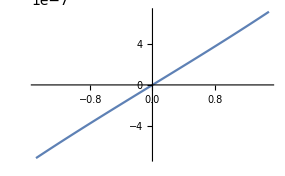

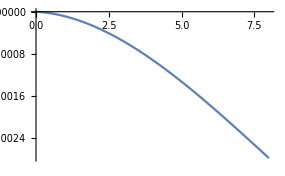

```mathematica
Plot[ux[L,y],{y,-Dh/2,Dh/2}]
Plot[uy[x,0],{x,0,L}]
```

```mathematica
uxList=Table[{y+Dh/2,-ux[L,y]},{y,-Dh/2,Dh/2,Dh/40}];
uyList=Table[{x,-uy[x,0]},{x,0,L,L/40}];
```

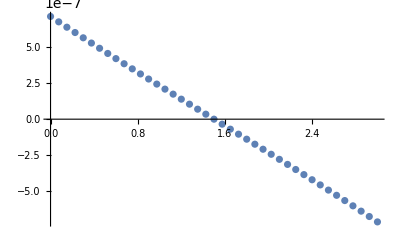

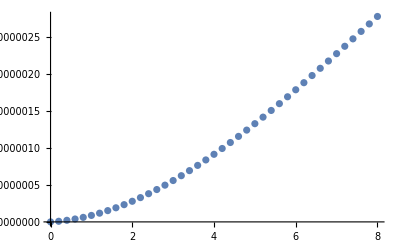

```mathematica
ListPlot[uxList]
ListPlot[uyList]
```

```mathematica
uxmax=ux[L,Dh/2](*exact solution for max (ux)*)
uymax=uy[L,Dh/2](*exact solution for max (uy)*)
```

7.11111×10^-7

-2.77284×10^-6

## Test with 41x16 particles or 81x31 particles

### Model meshed into 41x16 particles.

```mathematica
(*Create the model*)
xmin={0.,0.};xmax={8.,3.};
{width,height}=xmax-xmin;
dx=0.2;(*particle size.*)
coord=GridDomain[xmin+0.5dx,xmax-0.5 dx,dx];(*discretize the region into a list of particles.*)
mesh1=MyDelaunayMesh[coord];(*create the mesh from the particles, for showing field in post process*)
vol=ConstantArray[dx^2,Length[coord]];(*vol stores the volume of each particle.*)
Nnode=Length[coord];ndim=Length[coord[[1]]];
ndof=ndim Nnode;(*number of degrees of freedom.*)
(*define material parameters*)
Es=30 10^9;(*elastic modulus*)
mu=0.3;(*Poisson's ratio.*)
etype=2;(*1,plane stress,2,plane strain,3,3D*)(*etype=2, the plane strain is selected.*)

penCoef=0.3;(*penalty of hourglass energy.*)
numNei=6;(*We select 6 nearest neighbors for each particles. Larger number of neighbors is feasible*)
NeiList=Nearest[coord->Automatic,coord,numNei+1];(*find the 7 nearst neighbors of each particle.*)
WeiF[r_]:=1./r^2;(*other influence functions, weight functions, sph kernel functions will work*)
```

```mathematica
(*prepare the boundary conditions.*)
```

```mathematica
nfix=FindPoints[coord,xmin,xmin+{0.5dx,height}];(*find the particles for Dirichlet BCs.*)
fixdof=Flatten[{2 nfix-1,2nfix}];(*fix in x,y direction*)(*fixdof is the list of dof to be fixed.*)
nforce=FindPoints[coord,xmax-{0.5dx,height},xmax];(*find the particles for Neumann BCs.*)
forcedof=2nforce;(*force dof is only on y direction.*)
dofFix={fixdof,ConstantArray[0.,Length[fixdof]]};(*dof in y direction*)
forceY=1000./3;(*force per unit length.*)
dofForce={forcedof,ConstantArray[dx forceY,Length[forcedof]]};
```

```mathematica
Ksp=SparseArray[{},{ndof,ndof}];(*declare the sparse matrix.*)
Do[
ni=NeiIIndex[NeiList[[i]],ndim];(*get the global indices of the tangent matrix of one particle.*)
{Bmat,Hgmat}=BHgmatrix[coord[[NeiList[[i]]]],WeiF,vol[[NeiList[[i]]]]];
(*get the non-local gradient matrix and tangent matrix of hourglass energy*)
Ksp[[ni,ni]]+=Kmatrix[vol[[i]],Bmat,Hgmat,Es,mu,etype,penCoef];
(*Kmatrix returns the tangent stiffness matrix of one particle, which is assembled into the Ksp matrix.*)
,{i,Nnode}(*loop for all particles.*)
];
```

```mathematica
Rsp=ConstantArray[0.,ndof];(*declare the force vector.*)
pDirichlet=10^6;(*penalty in the enforcement of Dirichlet boundary conditions.*)
DirichletApply[Ksp,Rsp,dofFix,pDirichlet];(*Apply Dirichlet boundary conditions.*)
NeumannApply[Rsp,dofForce];(*Apply Neumann force boundary conditions.*)
```

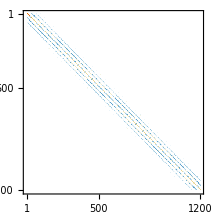

```mathematica
MatrixPlot[Ksp]
```

```mathematica
uv=LinearSolve[Ksp,Rsp];(*Solve the linear algebra equations and get the unknown vector.*)
uvw=Vector2Matrix[uv,ndim];(*convert vector to list of vectors.*)
```

```mathematica
uvw[[All,1]]//MinMax (*minimal and maximal displacement in x direction*)
uvw[[All,2]]//MinMax (*minimal and maximal displacement in y direction*)
```

{-6.37576×10^-7,6.64814×10^-7}

{-1.52618×10^-15,2.64425×10^-6}

```mathematica
(*(*exact solution*)uxmax=ux[L,Dh/2]=7.1111*^-7, uymax=uy[L,Dh/2]=-2.7728*^-6*)
```

40

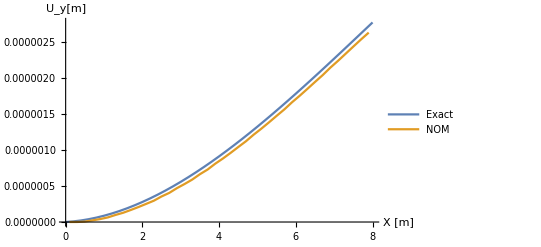

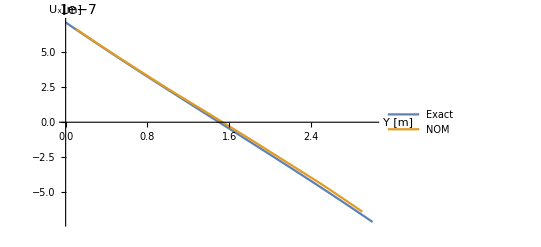

```mathematica
midPts=FindPoints[coord,{0,Dh/2}-0.1dx,{L,Dh/2}+0.1dx];Length[midPts]
ListPlot[{uyList,{coord[[midPts,1]],uvw[[midPts,2]]}ᵀ},Joined->True,PlotLegends->{"Exact","NOM"},AxesLabel->{"X [m]","U_y[m]"}]
ListPlot[{uxList,{coord[[nforce,2]],uvw[[nforce,1]]}ᵀ},Joined->True,PlotLegends->{"Exact","NOM"},AxesLabel->{"Y [m]","U_x[m]"}]
```

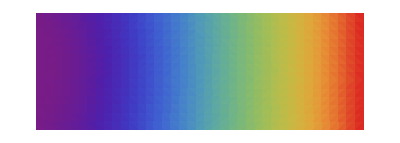

```mathematica
Plot2DField[uvw[[All,2]],mesh1]
```

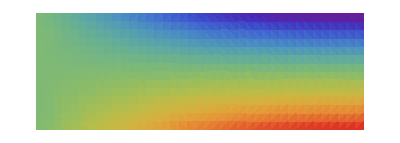

```mathematica
Plot2DField[uvw[[All,1]],mesh1]
```

```mathematica
Contour2DField[uvw[[All,2]],mesh1,11]
```

-Graphics-

```mathematica
Contour2DField[uvw[[All,1]],mesh1,11]
```

-Graphics-

### Model meshed into 81x31 particles.

```mathematica
(*Create the model*)
xmin={0.,0.};xmax={8.,3.};
{width,height}=xmax-xmin;
dx=0.1;(*particle size.*)
coord=GridDomain[xmin+{0.dx,0.5 dx},xmax-{0.0dx,0.5 dx},dx];
(*coord=GridDomain[xmin,xmax,dx];*)(*discretize the region into list of particles.*)
mesh1=MyDelaunayMesh[coord];(*create the mesh from the particles, for showing field in post process*)
vol=ConstantArray[dx^2,Length[coord]];(*vol stores the volume of each particle.*)
Nnode=Length[coord];ndim=Length[coord[[1]]];
ndof=ndim Nnode;(*number of degrees of freedom.*)
(*define material parameters*)
Es=30 10^9;(*elastic modulus*)
mu=0.3;(*Poisson's ratio.*)
etype=2;(*1,plane stress,2,plane strain,3,3D*)(*etype=2, the plane strain is selected.*)

penCoef=0.9;(*penalty of hourglass energy.*)
numNei=6;(*We select 6 nearest neighbors for each particles.*)
NeiList=Nearest[coord->Automatic,coord,numNei+1];(*find the 7 nearst neighbors of each particle.*)
WeiF[r_]:=1./r^2;(*other influence functions, weight functions, sph kernel functions work*)
```

```mathematica
(*prepare the boundary conditions.*)
```

```mathematica
nfix=FindPoints[coord,xmin,xmin+{0.5dx,height}];(*find the particles for Dirichlet BCs.*)
fixdof=Flatten[{2 nfix-1,2nfix}];(*fix in x,y direction*)(*fixdof is the list of dof to be fixed.*)
nforce=FindPoints[coord,xmax-{0.5dx,height},xmax];(*find the particles for Neumann BCs.*)
forcedof=2nforce;(*force dof is only on y direction.*)
dofFix={fixdof,ConstantArray[0.,Length[fixdof]]};(*dof in y direction*)
forceY=1000./3;(*force per unit length.*)
dofForce={forcedof,ConstantArray[dx forceY,Length[forcedof]]};
```

```mathematica
Ksp=SparseArray[{},{ndof,ndof}];(*declare the sparse matrix.*)
Do[
ni=NeiIIndex[NeiList[[i]],ndim];(*get the global indices of the tangent matrix of one particle.*)
{Bmat,Hgmat}=BHgmatrix[coord[[NeiList[[i]]]],WeiF,vol[[NeiList[[i]]]]];
(*get the non-local gradient matrix and tangent matrix of hourglass energy*)
Ksp[[ni,ni]]+=Kmatrix[vol[[i]],Bmat,Hgmat,Es,mu,etype,penCoef];
(*Kmatrix returns the tangent stiffness matrix of one particle, which is assembled into the Ksp matrix.*)
,{i,Nnode}(*loop for all particles.*)
];
```

```mathematica
Rsp=ConstantArray[0.,ndof];(*declare the force vector.*)
pDirichlet=10^6;(*penalty in the enforcement of Dirichlet boundary conditions.*)
DirichletApply[Ksp,Rsp,dofFix,pDirichlet];(*Apply Dirichlet boundary conditions.*)
NeumannApply[Rsp,dofForce];(*Apply Neumann force boundary conditions.*)
```

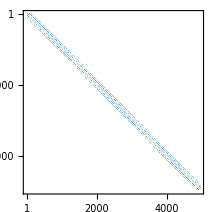

```mathematica
MatrixPlot[Ksp]
```

```mathematica
uv=LinearSolve[Ksp,Rsp];(*Solve the linear algebra equations and get the unknown vector.*)
uvw=Vector2Matrix[uv,ndim];(*convert vector to list of vectors.*)
```

```mathematica
uvw[[All,1]]//MinMax (*minimal and maximal displacement in x direction*)
uvw[[All,2]]//MinMax (*minimal and maximal displacement in y direction*)
```

{-6.98327×10^-7,6.93415×10^-7}

{-5.6408×10^-16,2.78328×10^-6}

```mathematica
(*(*exact solution*)uxmax=ux[L,Dh/2]=7.1111*^-7, uymax=uy[L,Dh/2]=-2.7728*^-6*)
```

81

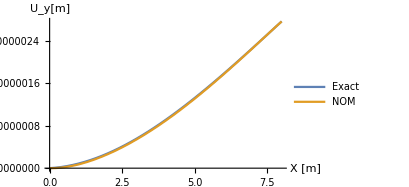

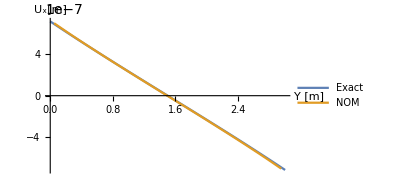

```mathematica
midPts=FindPoints[coord,{0,Dh/2}-0.1dx,{L,Dh/2}+0.1dx];Length[midPts]
ListPlot[{uyList,{coord[[midPts,1]],uvw[[midPts,2]]}ᵀ},Joined->True,PlotLegends->{"Exact","NOM"},AxesLabel->{"X [m]","U_y[m]"}]
ListPlot[{uxList,{coord[[nforce,2]],uvw[[nforce,1]]}ᵀ},Joined->True,PlotLegends->{"Exact","NOM"},AxesLabel->{"Y [m]","U_x[m]"}]
```

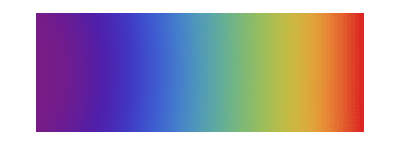

```mathematica
Plot2DField[uvw[[All,2]],mesh1]
```

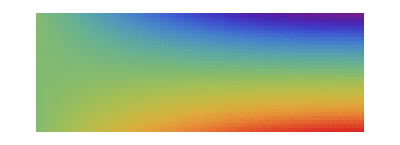

```mathematica
Plot2DField[uvw[[All,1]],mesh1]
```

```mathematica
Contour2DField[uvw[[All,2]],mesh1,11]
```

-Graphics-

```mathematica
Contour2DField[uvw[[All,1]],mesh1,9]
```

-Graphics-